### Start choosing the example:

```mathematica
Needs["MFGraphs`"]
```

```mathematica
t=14;
beta = 1;
A =0;
g[x]
```

g[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
```

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

InitRules

Simplifying SC...

SSC done!

Solving some balances: jt8==jt1+jt2&&jt14+jt9==jt3+jt4&&3==jt5+jt6&&jt3+jt5==jt7&&jt11+jt13==jt8&&jt7==jt10+jt9&&jt1+jt6==jt11+jt12&&0==jt13+jt14&&u9==u10&&u7==1

TripleClean...
{u1==u6&&u4==u5,jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&u1≥u10&&u10≤u6&&u2≤1/2+u3&&u3≤u2&&u4≤u7&&u5≤u7,(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(jt1==0||jt3==0)&&(jt10==0||jt13==0)&&(jt11==0||jt9==0)&&(jt12==0||jt14==0)&&(jt2==0||jt5==0)&&(jt4==0||jt6==0)&&(jt7==0||jt8==0)&&(jt1==0||-u1+u6==0)&&jt2==0&&(jt3==0||u1-u6==0)&&jt4==0&&(jt5==0||u1-u10==0)&&(jt6==0||-u10+u6==0)&&(jt7==0||1/2-u2+u3==0)&&(jt8==0||u2-u3==0)&&(jt9==0||-u4+u5==0)&&(jt10==0||-u4+u7==0)&&(jt11==0||u4-u5==0)&&(jt12==0||-u5+u7==0)&&jt13==0&&jt14==0}

TripleStep 1: u1==u6&&u4==u5

TripleStep 1.5: jt1≥0&&-jt1+jt11+jt13≥0&&jt3≥0&&jt4≥0&&jt10+jt13+jt4≥0&&3-jt10-jt13-jt4≥0&&jt10+jt13+jt3+jt4≥0&&jt11+jt13≥0&&jt13+jt3+jt4≥0&&jt10≥0&&jt11≥0&&3+jt1-jt10-jt11-jt13-jt4≥0&&jt13≥0&&-jt13≥0&&jt11+jt13≥0&&jt10+jt13+jt3+jt4≥0&&jt11+jt13≥0&&jt10+jt13+jt3+jt4≥0&&3+jt1-jt10-jt13-jt4≥0&&jt3+jt4≥0&&3+jt1-jt11-jt13-jt4≥0&&-jt1+jt11+jt13+jt4≥0&&u1≥u10&&u10≤u1&&u2≤1/2+u3&&u3≤u2&&u4≤1&&u4≤1

TripleStep 2: (jt11+jt13==0||jt10+jt13+jt3+jt4==0)&&(jt11+jt13==0||jt10+jt13+jt3+jt4==0)&&(3+jt1-jt10-jt13-jt4==0||jt3+jt4==0)&&-jt1+jt11+jt13+jt4==0&&(jt1==0||jt3==0)&&(jt10==0||jt13==0)&&(jt11==0||jt13+jt3+jt4==0)&&(3+jt1-jt10-jt11-jt13-jt4==0||-jt13==0)&&(-jt1+jt11+jt13==0||jt10+jt13+jt4==0)&&(jt4==0||3-jt10-jt13-jt4==0)&&(jt10+jt13+jt3+jt4==0||jt11+jt13==0)&&(jt1==0||-u1+u6==0)&&-jt1+jt11+jt13==0&&(jt3==0||u1-u6==0)&&jt4==0&&(jt10+jt13+jt4==0||u1-u10==0)&&(3-jt10-jt13-jt4==0||-u10+u6==0)&&(jt10+jt13+jt3+jt4==0||1/2-u2+u3==0)&&(jt11+jt13==0||u2-u3==0)&&(jt13+jt3+jt4==0||-u4+u5==0)&&(jt10==0||1-u4==0)&&(jt11==0||u4-u5==0)&&(3+jt1-jt10-jt11-jt13-jt4==0||1-u5==0)&&jt13==0&&-jt13==0

TripleStep 1: -jt1+jt11+jt13+jt4==0&&-jt1+jt11+jt13==0&&jt4==0&&jt13==0&&-jt13==0

TripleStep 1.5: jt1≥0&&jt3≥0&&jt10≥0&&3-jt10≥0&&jt10+jt3≥0&&jt1≥0&&jt3≥0&&jt10≥0&&jt1≥0&&3-jt10≥0&&jt1≥0&&jt10+jt3≥0&&jt1≥0&&jt10+jt3≥0&&3+jt1-jt10≥0&&jt3≥0&&u1≥u10&&u10≤u1&&u2≤1/2+u3&&u3≤u2&&u4≤1&&u4≤1

TripleStep 2: (jt11+jt13==0||jt10+jt13+jt3+jt4==0)&&(jt11+jt13==0||jt10+jt13+jt3+jt4==0)&&(3+jt1-jt10-jt13-jt4==0||jt3+jt4==0)&&(jt1==0||jt3==0)&&(jt10==0||jt13==0)&&(jt11==0||jt13+jt3+jt4==0)&&(3+jt1-jt10-jt11-jt13-jt4==0||-jt13==0)&&(-jt1+jt11+jt13==0||jt10+jt13+jt4==0)&&(jt4==0||3-jt10-jt13-jt4==0)&&(jt10+jt13+jt3+jt4==0||jt11+jt13==0)&&(jt10+jt13+jt4==0||u1-u10==0)&&(3-jt10-jt13-jt4==0||u1-u10==0)&&(jt10+jt13+jt3+jt4==0||1/2-u2+u3==0)&&(jt11+jt13==0||u2-u3==0)&&(jt10==0||1-u4==0)&&(3+jt1-jt10-jt11-jt13-jt4==0||1-u4==0)

Preprocessing: NewSystem after first TripleClean: {True,jt1≥0&&jt3≥0&&jt10≥0&&3-jt10≥0&&jt10+jt3≥0&&jt1≥0&&jt3≥0&&jt10≥0&&jt1≥0&&3-jt10≥0&&jt1≥0&&jt10+jt3≥0&&jt1≥0&&jt10+jt3≥0&&3+jt1-jt10≥0&&jt3≥0&&u1≥u10&&u10≤u1&&u2≤1/2+u3&&u3≤u2&&u4≤1&&u4≤1,(jt11+jt13==0||jt10+jt13+jt3+jt4==0)&&(jt11+jt13==0||jt10+jt13+jt3+jt4==0)&&(3+jt1-jt10-jt13-jt4==0||jt3+jt4==0)&&(jt1==0||jt3==0)&&(jt10==0||jt13==0)&&(jt11==0||jt13+jt3+jt4==0)&&(3+jt1-jt10-jt11-jt13-jt4==0||-jt13==0)&&(-jt1+jt11+jt13==0||jt10+jt13+jt4==0)&&(jt4==0||3-jt10-jt13-jt4==0)&&(jt10+jt13+jt3+jt4==0||jt11+jt13==0)&&(jt10+jt13+jt4==0||u1-u10==0)&&(3-jt10-jt13-jt4==0||u1-u10==0)&&(jt10+jt13+jt3+jt4==0||1/2-u2+u3==0)&&(jt11+jt13==0||u2-u3==0)&&(jt10==0||1-u4==0)&&(3+jt1-jt10-jt11-jt13-jt4==0||1-u4==0)}

TripleClean again (with some more equalities)...

TripleStep 1: -jt1+jt10+jt3-u1+u2==cpc1&&-jt1+jt10+jt3-u3+u4==cpc2&&-3-jt1+jt10+jt3+u1-u4==cpc3

TripleStep 1.5: jt1≥0&&jt3≥0&&jt10≥0&&3-jt10≥0&&jt10+jt3≥0&&3+jt1-jt10≥0&&u1≥u10&&u10≤u1&&cpc1+jt1-jt10-jt3+u1≤-5/2-cpc2-cpc3-2 jt1+2 jt10+2 jt3+u1&&-3-cpc2-cpc3-2 jt1+2 jt10+2 jt3+u1≤cpc1+jt1-jt10-jt3+u1&&-3-cpc3-jt1+jt10+jt3+u1≤1

TripleStep 2: (jt1==0||jt10+jt3==0)&&(3+jt1-jt10==0||jt3==0)&&(jt1==0||jt3==0)&&(jt1==0||jt3==0)&&(jt10+jt3==0||jt1==0)&&(jt10==0||u1-u10==0)&&(3-jt10==0||u1-u10==0)&&(jt10+jt3==0||1/2-u2+u3==0)&&(jt1==0||u2-u3==0)&&(jt10==0||1-u4==0)&&(3-jt10==0||1-u4==0)

Preprocessing: NewSystem after second TripleClean: {True,jt1≥0&&jt3≥0&&jt10≥0&&3-jt10≥0&&jt10+jt3≥0&&3+jt1-jt10≥0&&u1≥u10&&u10≤u1&&cpc1+jt1-jt10-jt3+u1≤-5/2-cpc2-cpc3-2 jt1+2 jt10+2 jt3+u1&&-3-cpc2-cpc3-2 jt1+2 jt10+2 jt3+u1≤cpc1+jt1-jt10-jt3+u1&&-3-cpc3-jt1+jt10+jt3+u1≤1,(jt1==0||jt10+jt3==0)&&(3+jt1-jt10==0||jt3==0)&&(jt1==0||jt3==0)&&(jt1==0||jt3==0)&&(jt10+jt3==0||jt1==0)&&(jt10==0||u1-u10==0)&&(3-jt10==0||u1-u10==0)&&(jt10+jt3==0||1/2-u2+u3==0)&&(jt1==0||u2-u3==0)&&(jt10==0||1-u4==0)&&(3-jt10==0||1-u4==0)}

Preprocessing took 0.08285 seconds to terminate.

Starting Solver

Replaced: {True,jt1≥0&&jt3≥0&&jt10≥0&&jt10≤3&&jt10+jt3≥0&&3+jt1≥jt10&&u1≥u10&&u10≤u1&&5/2+3 jt1+u1≤3 jt10+3 jt3+u1&&3 (jt10+jt3)≤3+3 jt1&&jt10+jt3+u1≤4+jt1,(jt1==0||jt10+jt3==0)&&(3+jt1==jt10||jt3==0)&&(jt1==0||jt3==0)&&(jt10+jt3==0||jt1==0)&&(jt10==0||u1==u10)&&(jt10==3||u1==u10)&&(jt10+jt3==0||1/2+u3==u2)&&(jt1==0||u2==u3)&&(jt10==0||u4==1)&&(jt10==3||u4==1)}

Feeding this to FinalStep:
{True,jt1≥0&&jt10≤3&&jt10≥0&&5/6+jt1≤jt10+jt3&&1+jt1≥jt10+jt3&&jt3≥0&&4+jt1≥jt10+jt3+u1&&u1≥u10,(jt1==0||jt3==0)&&(jt1==0||u2==u3)&&(jt10==0||u1==u10)&&(jt10==0||u4==1)&&(jt10==3||u1==u10)&&(jt10==3||u4==1)&&(jt1==0||jt10+jt3==0)&&(3+jt1==jt10||jt3==0)&&(jt10+jt3==0||jt1==0)&&(jt10+jt3==0||1/2+u3==u2)}

Iterative DNF convertion took 0.032355 seconds to terminate.

Reducing (each alternative) took 0.144979 seconds to terminate.

FinalStep 1: {True,True,(jt1==0&&jt10==5/6&&jt3==0&&u1==u10&&u10==19/6&&u2==1/2+u3&&u4==1)||(jt1==0&&jt3==0&&u1==u10&&u2==1/2+u3&&u4==1&&5/6≤jt10≤1&&u10≤3)||(jt1==0&&jt3==0&&u1==u10&&u2==1/2+u3&&u4==1&&5/6≤jt10≤4-u10&&3<u10<19/6)}

Iterative DNF convertion took 0.029371 seconds to terminate.

Reducing (each alternative) took 0.006628 seconds to terminate.

MFGSS: (Possibly) Multiple solutions: (jt1==0.&&jt3==0.&&u2==0.5+u3&&u4==1.&&6. jt10==5.&&6. u1==19.&&6. u10==19.)||(6. jt10≥5.&&jt1==0.&&jt3==0.&&u2==0.5+u3&&u4==1.&&u1==u10&&jt10≤1.&&u10≤3.)||(jt1==0.&&jt3==0.&&u2==0.5+u3&&u4==1.&&6. jt10==5.&&u1==u10&&3.<u10&&6. u10<19.)||(6. jt10>5.&&jt1==0.&&jt3==0.&&u2==0.5+u3&&u4==1.&&u1==u10&&3.<u10&&6. u10<19.&&jt10+u10≤4.)

{}

Picked one value for the variable(s) {u1,u2,u3,u4,u10,jt1,jt3,jt10} {3.16667,0.,-0.5,1.,3.16667,0.,0.,0.833333} (respectively)

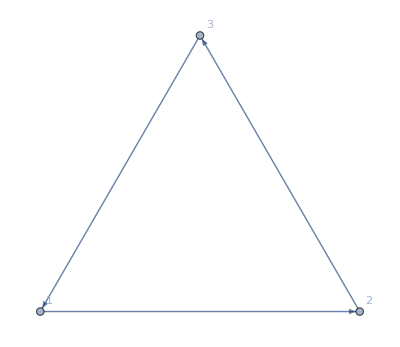
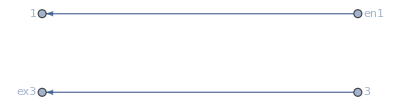
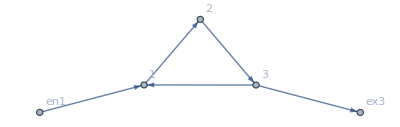
{0.520293,<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}},VL→{1,2,3},AM→{{0,1,0},{0,0,1},{1,0,0}},EVC→{{1,3}},EVTC→{{3,1}},SC→{{1,2,3,1/2},{3,2,1,0}},BG→-Graphics-,EntranceVertices→{1},InwardVertices→<|1→en1|>,ExitVertices→{3},OutwardVertices→<|3→ex3|>,InEdges→{en1->1},OutEdges→{3->ex3},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->2,2->3,3->1,3->ex3,en1->1},BEL→{1->2,2->3,3->1},FVL→{1,2,3,en1,ex3},jargs→{{1,1->2},{2,1->2},{2,2->3},{3,2->3},{3,3->1},{1,3->1},{3,3->ex3},{ex3,3->ex3},{en1,en1->1},{1,en1->1}},uargs→{{1,1->2},{2,1->2},{2,2->3},{3,2->3},{3,3->1},{1,3->1},{3,3->ex3},{ex3,3->ex3},{en1,en1->1},{1,en1->1}},AllTransitions→{{1,1->2,3->1},{1,1->2,en1->1},{1,3->1,1->2},{1,3->1,en1->1},{1,en1->1,1->2},{1,en1->1,3->1},{2,1->2,2->3},{2,2->3,1->2},{3,2->3,3->1},{3,2->3,3->ex3},{3,3->1,2->3},{3,3->1,3->ex3},{3,3->ex3,2->3},{3,3->ex3,3->1}},EntryArgs→{{1,en1->1}},EntryDataAssociation→<|{1,en1->1}→3|>,ExitCosts→<|ex3→1|>,js→{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10},jvars→<|{1,1->2}→j1,{2,1->2}→j2,{2,2->3}→j3,{3,2->3}→j4,{3,3->1}→j5,{1,3->1}→j6,{3,3->ex3}→j7,{ex3,3->ex3}→j8,{en1,en1->1}→j9,{1,en1->1}→j10|>,us→{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10},uvars→<|{1,1->2}→u1,{2,1->2}→u2,{2,2->3}→u3,{3,2->3}→u4,{3,3->1}→u5,{1,3->1}→u6,{3,3->ex3}→u7,{ex3,3->ex3}→u8,{en1,en1->1}→u9,{1,en1->1}→u10|>,jts→{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10,jt11,jt12,jt13,jt14},jtvars→<|{1,1->2,3->1}→jt1,{1,1->2,en1->1}→jt2,{1,3->1,1->2}→jt3,{1,3->1,en1->1}→jt4,{1,en1->1,1->2}→jt5,{1,en1->1,3->1}→jt6,{2,1->2,2->3}→jt7,{2,2->3,1->2}→jt8,{3,2->3,3->1}→jt9,{3,2->3,3->ex3}→jt10,{3,3->1,2->3}→jt11,{3,3->1,3->ex3}→jt12,{3,3->ex3,2->3}→jt13,{3,3->ex3,3->1}→jt14|>,SignedCurrents→<|1->2→-j1+j2,2->3→-j3+j4,3->1→-j5+j6,3->ex3→-j7+j8,en1->1→j10-j9|>,SwitchingCosts→<|{1,1->2,3->1}→0,{1,1->2,en1->1}→∞,{1,3->1,1->2}→0,{1,3->1,en1->1}→∞,{1,en1->1,1->2}→0,{1,en1->1,3->1}→0,{2,1->2,2->3}→1/2,{2,2->3,1->2}→0,{3,2->3,3->1}→0,{3,2->3,3->ex3}→0,{3,3->1,2->3}→0,{3,3->1,3->ex3}→0,{3,3->ex3,2->3}→∞,{3,3->ex3,3->1}→∞|>,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0,EqPosJts→jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0),EqTransitionCompCon→(jt1==0||jt3==0)&&(jt10==0||jt13==0)&&(jt11==0||jt9==0)&&(jt12==0||jt14==0)&&(jt2==0||jt5==0)&&(jt4==0||jt6==0)&&(jt7==0||jt8==0),NoDeadEnds→{{1,1->2},{1,3->1},{1,en1->1},{2,1->2},{2,2->3},{3,2->3},{3,3->1},{3,3->ex3}},EqBalanceSplittingCurrents→j1==jt1+jt2&&j6==jt3+jt4&&j10==jt5+jt6&&j2==jt7&&j3==jt8&&j4==jt10+jt9&&j5==jt11+jt12&&j7==jt13+jt14,BalanceSplittingCurrents→{j1-jt1-jt2,j6-jt3-jt4,j10-jt5-jt6,j2-jt7,j3-jt8,j4-jt10-jt9,j5-jt11-jt12,j7-jt13-jt14},NoDeadStarts→{{2,1->2},{3,3->1},{en1,en1->1},{1,1->2},{3,2->3},{2,2->3},{1,3->1},{ex3,3->ex3}},RuleBalanceGatheringCurrents→<|j2→jt3+jt5,j5→jt1+jt6,j9→jt2+jt4,j1→jt8,j4→jt7,j3→jt11+jt13,j6→jt14+jt9,j8→jt10+jt12|>,BalanceGatheringCurrents→{-j2+jt3+jt5,-j5+jt1+jt6,-j9+jt2+jt4,-j1+jt8,-j4+jt7,-j3+jt11+jt13,-j6+jt14+jt9,-j8+jt10+jt12},EqBalanceGatheringCurrents→j2==jt3+jt5&&j5==jt1+jt6&&j9==jt2+jt4&&j1==jt8&&j4==jt7&&j3==jt11+jt13&&j6==jt14+jt9&&j8==jt10+jt12,EqEntryIn→{j10==3},RuleEntryOut→<|j9→0|>,RuleExitCurrentsIn→<|j7→0|>,RuleExitValues→<|u8→1|>,EqValueAuxiliaryEdges→u9==u10&&u7==u8,OutRules→{{3,3->ex3,1->2}→∞,{3,3->ex3,2->3}→∞,{3,3->ex3,3->1}→∞,{3,3->ex3,3->ex3}→∞,{3,3->ex3,en1->1}→∞},InRules→{{1,1->2,en1->1}→∞,{1,3->1,en1->1}→∞,{1,en1->1,en1->1}→∞},EqSwitchingByVertex→{u1≤u6&&u6≤u1&&u10≤u1&&u10≤u6,u2≤1/2+u3&&u3≤u2,u4≤u5&&u4≤u7&&u5≤u4&&u5≤u7},EqCompCon→(jt1==0||-u1+u6==0)&&jt2==0&&(jt3==0||u1-u6==0)&&jt4==0&&(jt5==0||u1-u10==0)&&(jt6==0||-u10+u6==0)&&(jt7==0||1/2-u2+u3==0)&&(jt8==0||u2-u3==0)&&(jt9==0||-u4+u5==0)&&(jt10==0||-u4+u7==0)&&(jt11==0||u4-u5==0)&&(jt12==0||-u5+u7==0)&&jt13==0&&jt14==0,Nlhs→{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6},CostArgs→<|{1,1->2}→j1 j2+Abs[IntM[-j1+j2,1->2]],{2,1->2}→j1 j2+Abs[IntM[-j1+j2,1->2]],{2,2->3}→j3 j4+Abs[IntM[-j3+j4,2->3]],{3,2->3}→j3 j4+Abs[IntM[-j3+j4,2->3]],{3,3->1}→j5 j6+Abs[IntM[-j5+j6,3->1]],{1,3->1}→j5 j6+Abs[IntM[-j5+j6,3->1]],{3,3->ex3}→j7 j8+Abs[IntM[-j7+j8,3->ex3]],{ex3,3->ex3}→0,{en1,en1->1}→j10 j9+Abs[IntM[j10-j9,en1->1]],{1,en1->1}→0,{1,1->2,3->1}→jt1 jt3,{1,1->2,en1->1}→1000000+jt2 jt5,{1,3->1,1->2}→jt1 jt3,{1,3->1,en1->1}→1000000+jt4 jt6,{1,en1->1,1->2}→jt2 jt5,{1,en1->1,3->1}→jt4 jt6,{2,1->2,2->3}→1/2+jt7 jt8,{2,2->3,1->2}→jt7 jt8,{3,2->3,3->1}→jt11 jt9,{3,2->3,3->ex3}→jt10 jt13,{3,3->1,2->3}→jt11 jt9,{3,3->1,3->ex3}→jt12 jt14,{3,3->ex3,2->3}→1000000+jt10 jt13,{3,3->ex3,3->1}→1000000+jt12 jt14|>,Nrhs→{-j1+j2-IntM[-j1+j2,1->2] Sign[-j1+j2],-j3+j4-IntM[-j3+j4,2->3] Sign[-j3+j4],-j5+j6-IntM[-j5+j6,3->1] Sign[-j5+j6]},costpluscurrents→<|cpc1→-j1+j2-IntM[-j1+j2,1->2] Sign[-j1+j2],cpc2→-j3+j4-IntM[-j3+j4,2->3] Sign[-j3+j4],cpc3→-j5+j6-IntM[-j5+j6,3->1] Sign[-j5+j6]|>,EqGeneral→-j1+j2-u1+u2==cpc1&&-j3+j4-u3+u4==cpc2&&-j5+j6-u5+u6==cpc3,CostArgs2→<|{1,1->2}→1/1000000+Abs[j1]+Abs[j2],{2,1->2}→1/1000000+Abs[j1]+Abs[j2],{2,2->3}→1/1000000+Abs[j3]+Abs[j4],{3,2->3}→1/1000000+Abs[j3]+Abs[j4],{3,3->1}→1/1000000+Abs[j5]+Abs[j6],{1,3->1}→1/1000000+Abs[j5]+Abs[j6],{3,3->ex3}→1/1000000+Abs[j7]+Abs[j8],{ex3,3->ex3}→0,{en1,en1->1}→1/1000000+Abs[j10]+Abs[j9],{1,en1->1}→0,{1,1->2,3->1}→Abs[jt1]+Abs[jt3],{1,1->2,en1->1}→1000000+Abs[jt2]+Abs[jt5],{1,3->1,1->2}→Abs[jt1]+Abs[jt3],{1,3->1,en1->1}→1000000+Abs[jt4]+Abs[jt6],{1,en1->1,1->2}→Abs[jt2]+Abs[jt5],{1,en1->1,3->1}→Abs[jt4]+Abs[jt6],{2,1->2,2->3}→1/2+Abs[jt7]+Abs[jt8],{2,2->3,1->2}→Abs[jt7]+Abs[jt8],{3,2->3,3->1}→Abs[jt11]+Abs[jt9],{3,2->3,3->ex3}→Abs[jt10]+Abs[jt13],{3,3->1,2->3}→Abs[jt11]+Abs[jt9],{3,3->1,3->ex3}→Abs[jt12]+Abs[jt14],{3,3->ex3,2->3}→1000000+Abs[jt10]+Abs[jt13],{3,3->ex3,3->1}→1000000+Abs[jt12]+Abs[jt14]|>,InitRules→<|j10→3,j9→0,j7→0,j2→jt10+jt3,j5→3+jt1-jt10,j1→jt1,j4→jt10+jt3,j3→jt1,j6→jt3,j8→3,u8→1,jt12→3-jt10,jt14→0,jt2→0,jt5→jt10,jt6→3-jt10,jt7→jt10+jt3,jt8→jt1,jt9→jt3,u7→1,u9→u10,u5→-3-cpc3-jt1+jt10+jt3+u1,u6→u1,jt11→jt1,jt13→0,jt4→0,u2→cpc1+jt1-jt10-jt3+u1,u3→-3-cpc2-cpc3-2 jt1+2 jt10+2 jt3+u1,u4→-3-cpc3-jt1+jt10+jt3+u1|>,NewSystem→{True,jt1≥0&&jt3≥0&&jt10≥0&&jt10≤3&&jt10+jt3≥0&&3+jt1≥jt10&&u1≥u10&&u10≤u1&&5/2+cpc1+cpc2+cpc3+3 jt1+u1≤3 jt10+3 jt3+u1&&3 (jt10+jt3)≤3+cpc1+cpc2+cpc3+3 jt1&&jt10+jt3+u1≤4+cpc3+jt1,(jt1==0||jt10+jt3==0)&&(3+jt1==jt10||jt3==0)&&(jt1==0||jt3==0)&&(jt10+jt3==0||jt1==0)&&(jt10==0||u1==u10)&&(jt10==3||u1==u10)&&(jt10+jt3==0||1/2+u3==u2)&&(jt1==0||u2==u3)&&(jt10==0||u4==1)&&(jt10==3||u4==1)},AssoCritical→<|u1→19/6,u2→0,u3→-1/2,u4→1,u5→1,u6→19/6,u7→1,u8→1,u9→19/6,u10→19/6,j1→0,j2→5/6,j3→0,j4→5/6,j5→13/6,j6→0,j7→0,j8→3,j9→0,j10→3,jt1→0,jt2→0,jt3→0,jt4→0,jt5→5/6,jt6→13/6,jt7→5/6,jt8→0,jt9→0,jt10→5/6,jt11→0,jt12→13/6,jt13→0,jt14→0|>|>}

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,1,0},{0,0,1},{1,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>;
(crit=CriticalCongestionSolver[d2e=Data2Equations[Data/.{I1->3,U1->1,S1->1/2, S2->0}]])//AbsoluteTiming
```

```mathematica
d2e["FG"]
```

-Graphics-

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->3,U1->1,S1->1/2, S2->0}]])//AbsoluteTiming
```

Variables are all set

CleanEqualities for the values at the auxiliary edges

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

CCS2: EliminateVarsSimplify for the us

CCS2: Not finished with the us!

(jt1==0||jt3==0)&&(jt1==0||jt10==-jt3)&&(jt1==0||jt1==-1+jt10+jt3)&&(jt3==0||jt1==-3+jt10)&&(jt10==-jt3||jt1==-5/6+jt10+jt3)&&jt10≤3&&jt1≤1/6 (-5+6 jt10+6 jt3)&&jt1≥0&&jt10≥-jt3&&jt1≥-3+jt10&&jt3≥0&&jt10≥0&&jt1≥-1+jt10+jt3

(jt1==0||jt3==0)&&(jt1==0||jt10==-jt3)&&(jt1==0||jt1==-1+jt10+jt3)&&(jt1==-3+jt10||jt3==0)&&(jt1==-5/6+jt10+jt3||jt10==-jt3)&&jt10≤3&&jt1≤1/6 (-5+6 jt10+6 jt3)&&jt1≥0&&jt10≥-jt3&&jt1≥-3+jt10&&jt3≥0&&jt10≥0&&jt1≥-1+jt10+jt3

CCS2: Reducing further (NewReduce)...

CCS2: Simplifying...

CCS2: Finished with the us!

CCS2: Finished with the js!

{0.099935,<|u1→19/6,u2→7/3,u3→11/6,u4→1,u5→1,u6→19/6,u7→1,u8→1,u9→19/6,u10→19/6,j1→0,j2→5/6,j3→0,j4→5/6,j5→13/6,j6→0,j7→0,j8→3,j9→0,j10→3|>}

## Non-critical congestion

```mathematica
Cost[current_,edge_]
```

IntM[current_,edge_]

```mathematica
Cost[a_,b_]:= -a
```

```mathematica
Cost[a_,b_]:= 0
```

```mathematica
d2e=D2E[Data/.{I1->3,U1->1,S1->1/2, S2->0}];
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

```mathematica
alpha =0;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

<|u1→1743525561/625000000,u2→2681025561/1250000000,u3→2056025561/1250000000,u4→1,u5→1,u6→1743525561/625000000,u7→1,u8→1,u9→1743525561/625000000,u10→1743525561/625000000,j1→0,j2→335140119/2500000000,j3→0,j4→335140119/2500000000,j5→7164859881/2500000000,j6→0,j7→0,j8→3,j9→0,j10→3|>

```mathematica
alpha =0.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

<|u1→44936296531/15000000000,u2→67436296531/30000000000,u3→52436296531/30000000000,u4→1,u5→1,u6→44936296531/15000000000,u7→1,u8→1,u9→44936296531/15000000000,u10→44936296531/15000000000,j1→0,j2→2934436247/6000000000,j3→0,j4→2934436247/6000000000,j5→15065563753/6000000000,j6→0,j7→0,j8→3,j9→0,j10→3|>

```mathematica
alpha =1;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

<|u1→19/6,u2→7/3,u3→11/6,u4→1,u5→1,u6→19/6,u7→1,u8→1,u9→19/6,u10→19/6,j1→0,j2→5/6,j3→0,j4→5/6,j5→13/6,j6→0,j7→0,j8→3,j9→0,j10→3|>

```mathematica
alpha =1.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

<|u1→16676465169/5000000000,u2→24176465169/10000000000,u3→19176465169/10000000000,u4→1,u5→1,u6→16676465169/5000000000,u7→1,u8→1,u9→16676465169/5000000000,u10→16676465169/5000000000,j1→0,j2→10931926613/10000000000,j3→0,j4→10931926613/10000000000,j5→19068073387/10000000000,j6→0,j7→0,j8→3,j9→0,j10→3|>

```mathematica
alpha =2;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

<|u1→182047142663/7500000000,u2→193297142663/15000000000,u3→185797142663/15000000000,u4→1,u5→1,u6→182047142663/7500000000,u7→1,u8→1,u9→182047142663/7500000000,u10→182047142663/7500000000,j1→0,j2→329523523669/30000000000,j3→0,j4→329523523669/30000000000,j5→0,j6→239523523669/30000000000,j7→0,j8→3,j9→0,j10→3|>

### DataToEquations and the critical congestion solver

```mathematica
Clear["DataG"]
```

```mathematica
Data=
```

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->3,U1->1,S1->1/2, S2->0}];//Timing
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
```

DataToEquations: Triangle inequalities for switching costs: {True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.322694 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j15==0&&6 j20==13&&jt23==0&&6 u37==19&&6 u38==11&&u39==1&&6 u41==19
and the rules are:
<|j17→3,u45→1,j13→3+j15-j20+jt23,j14→3+j15-j20+jt23,j16→3,j18→jt23,j19→jt23,j21→0,j22→0,jt24→0,jt25→j15,jt26→0,jt27→3-j20+jt23,jt28→j20-jt23,jt29→3+j15-j20+jt23,jt30→jt23,jt31→j15,jt32→3-j20+jt23,jt33→jt23,jt34→j20-jt23,jt35→0,jt36→0,u40→1,u42→-3-j15+j20+u37,u43→-3-j15+j20+u38,u44→-j15+j20+u39,u46→u41|>

DataToEquations: Critical congestion solved.

all ok? up to here?

{j13-j18+IntM[j13-j18,1->2],j14-j19+IntM[j14-j19,2->3],j15-j20+IntM[j15-j20,3->1]}

DataToEquations: Done.

{0.35119,Null}

<|{1,1->2}→0,{1,3->1}→0,{1,en11->1}→3,{2,1->2}→5/6,{2,2->3}→0,{3,2->3}→5/6,{3,3->1}→13/6,{3,3->ex12}→0,{en11,en11->1}→0,{ex12,3->ex12}→3|>

<|{1,1->2}→19/6,{1,3->1}→19/6,{1,en11->1}→19/6,{2,1->2}→7/3,{2,2->3}→11/6,{3,2->3}→1,{3,3->1}→1,{3,3->ex12}→1,{en11,en11->1}→19/6,{ex12,3->ex12}→1|>

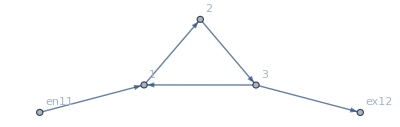

```mathematica
MFGEquations["FG"]
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j13-j18-u37+u42==-0.352298&&j14-j19-u38+u43==-0.352298&&j15-j20-u39+u44==-0.536342

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.352609

FRX1: nonlinear: 
j13-j18-u37+u42==-0.523617&&j14-j19-u38+u43==-0.523617&&j15-j20-u39+u44==-0.852218

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.135588

FRX1: nonlinear: 
j13-j18-u37+u42==-0.536848&&j14-j19-u38+u43==-0.536848&&j15-j20-u39+u44==-1.02405

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0493202

FRX1: nonlinear: 
j13-j18-u37+u42==-0.510782&&j14-j19-u38+u43==-0.510782&&j15-j20-u39+u44==-1.07628

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000300019

FRX1: nonlinear: 
j13-j18-u37+u42==-0.510762&&j14-j19-u38+u43==-0.510762&&j15-j20-u39+u44==-1.07631

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.14739×10^-6

FRX1: nonlinear: 
j13-j18-u37+u42==-0.510765&&j14-j19-u38+u43==-0.510765&&j15-j20-u39+u44==-1.0763

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.73574×10^-7

FRX1: nonlinear: 
j13-j18-u37+u42==-0.510764&&j14-j19-u38+u43==-0.510764&&j15-j20-u39+u44==-1.0763

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.93192×10^-8

<|j13→0.134056,j14→0.134056,j15→0,j16→3,j17→3,j18→0,j19→0,j20→2.86594,j21→0,j22→0,jt23→0,jt24→0,jt25→0,jt26→0,jt27→0.134056,jt28→2.86594,jt29→0.134056,jt30→0,jt31→0,jt32→0.134056,jt33→0,jt34→2.86594,jt35→0,jt36→0,u37→2.78964,u38→1.64482,u39→1.,u40→1,u41→2.78964,u42→2.14482,u43→1.,u44→2.78964,u45→1,u46→2.78964|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]]]]]]]]]]]

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]]]]]]]]]]]

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

```mathematica
alpha = 1.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

```mathematica
alpha = 1.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

```mathematica
alpha = 1.4;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

```mathematica
alpha = 1.77;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KeySort::invrl: The argument … is not a valid Association or a list of rules.

KeySort[FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]]

#### Test zone

```mathematica
alpha = 1.9;
FFR=FixedPointList[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧,FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧],FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]],FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]],FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]],FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]],FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]],FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]],FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]],FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]],FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]]]]]]}

```mathematica
((MFGEquations["jvars"]/.# &) )/@{<|j2733->3,u2761->1,j2729->5/6,j2730->5/6,j2732->3,j2734->0,j2735->0,j2737->0,j2738->0,jt2740->0,jt2741->0,jt2742->0,jt2743->5/6,jt2744->13/6,jt2745->5/6,jt2746->0,jt2747->0,jt2748->5/6,jt2749->0,jt2750->13/6,jt2751->0,jt2752->0,u2756->1,u2758->7/3,u2759->1,u2760->19/6,u2762->19/6,j2731->0,j2736->13/6,jt2739->0,u2753->19/6,u2754->11/6,u2755->1,u2757->19/6|>,<|j2733->3,u2761->1,j2729->1.8844732206260932,j2732->3,j2734->0,j2736->1.1155267793739068,j2737->0,j2738->0,jt2739->0,jt2740->0,jt2741->0,jt2742->0,jt2743->1.8844732206260932,jt2744->1.1155267793739068,jt2745->1.8844732206260932,jt2746->0,jt2747->0,jt2748->1.8844732206260932,jt2749->0,jt2750->1.1155267793739068,jt2751->0,jt2752->0,u2756->1,u2762->4.303706273221307,u2754->2.4018531366106535,u2755->1.,u2757->4.303706273221307,u2758->2.9018531366106526,u2759->1.,u2760->4.303706273221307,j2730->1.8844732206260932,j2731->0,j2735->0,u2753->4.303706273221306|>,<|j2733->3,u2761->1,j2729->0,j2732->3,j2734->0,j2736->3,j2737->0,j2738->0,jt2739->0,jt2740->0,jt2741->0,jt2742->0,jt2743->0,jt2744->3,jt2745->0,jt2746->0,jt2747->0,jt2748->0,jt2749->0,jt2750->3,jt2751->0,jt2752->0,u2756->1,u2762->3.6410922806342936,u2754->2.129945384029136,u2755->1.,u2757->3.6410922806342936,u2758->2.5111468966051578,u2759->1.,u2760->3.6410922806342936,j2730->0,j2731->0,j2735->0,u2753->3.6410922806342936|>,<|j2733->3,u2761->1,j2729->3.2566462770399003,j2732->3,j2734->0,j2736->-1.1102230246251565*^-16,j2737->0,j2738->0,jt2739->0,jt2740->0,jt2741->0.2566462770399002,jt2742->0,jt2743->3.,jt2744->-1.1102230246251565*^-16,jt2745->3.2566462770399003,jt2746->0,jt2747->0.2566462770399002,jt2748->3.,jt2749->0,jt2750->-1.1102230246251565*^-16,jt2751->0,jt2752->0,u2756->1,u2762->8.0132925540798,u2754->4.2566462770399,u2755->1.,u2757->8.0132925540798,u2758->4.7566462770399,u2759->1.,u2760->8.0132925540798,j2730->3.2566462770399003,j2731->0.2566462770399002,j2735->0,u2753->8.0132925540798|>,<|j2733->3,u2761->1,j2729->0,j2732->3,j2734->5.249421838611017,j2736->8.249421838611017,j2737->0,j2738->0,jt2739->5.249421838611017,jt2740->0,jt2741->0,jt2742->0,jt2743->0,jt2744->3,jt2745->0,jt2746->5.249421838611017,jt2747->0,jt2748->0,jt2749->5.249421838611017,jt2750->3,jt2751->0,jt2752->0,u2756->1,u2762->9.490346581588538,u2754->5.245173290794268,u2755->1.,u2757->9.490346581588538,u2758->5.24517329079427,u2759->1.,u2760->9.490346581588538,j2730->0,j2731->0,j2735->5.249421838611017,u2753->9.490346581588538|>,<|j2733->3,u2761->1,j2729->73.78534848283802,j2732->3,j2734->0,j2736->0.,j2737->0,j2738->0,jt2739->0,jt2740->0,jt2741->70.78534848283802,jt2742->0,jt2743->3.,jt2744->0.,jt2745->73.78534848283802,jt2746->0,jt2747->70.78534848283802,jt2748->3.,jt2749->0,jt2750->0.,jt2751->0,jt2752->0,u2756->1,u2762->69.78358079581146,u2754->35.14179039790574,u2755->1.,u2757->69.78358079581146,u2758->35.64179039790572,u2759->1.,u2760->69.78358079581146,j2730->73.78534848283802,j2731->70.78534848283802,j2735->0,u2753->69.78358079581146|>,<|j2733->3,u2761->1,j2729->0,j2732->3,j2734->45960.373286207345,j2736->45963.373286207345,j2737->0,j2738->0,jt2739->45960.373286207345,jt2740->0,jt2741->0,jt2742->0,jt2743->0,jt2744->3,jt2745->0,jt2746->45960.373286207345,jt2747->0,jt2748->0,jt2749->45960.373286207345,jt2750->3,jt2751->0,jt2752->0,u2756->1,u2762->3295.979899424623,u2754->1648.4899497123115,u2755->1.,u2757->3295.979899424623,u2758->1648.4899497123115,u2759->1.,u2760->3295.979899424623,j2730->0,j2731->0,j2735->45960.373286207345,u2753->3295.979899424624|>,<|j2733->3,u2761->1,j2729->1.1103657783306665*^12,j2732->3,j2734->0,j2736->0.,j2737->0,j2738->0,jt2739->0,jt2740->0,jt2741->1.1103657783276665*^12,jt2742->0,jt2743->3.,jt2744->0.,jt2745->1.1103657783306665*^12,jt2746->0,jt2747->1.1103657783276665*^12,jt2748->3.,jt2749->0,jt2750->0.,jt2751->0,jt2752->0,u2756->1,u2762->1.2738436671166992*^8,u2754->6.369218360595703*^7,u2755->1.,u2757->1.2738436671166992*^8,u2758->6.369218410573977*^7,u2759->1.,u2760->1.2738436671166992*^8,j2730->1.1103657783306665*^12,j2731->1.1103657783276665*^12,j2735->0,u2753->1.273843667116968*^8|>,<|j2733->3,u2761->1,j2729->0,j2732->3,j2734->3.2354258891387973*^31,j2736->3.2354258891387973*^31,j2737->0,j2738->0,jt2739->3.2354258891387973*^31,jt2740->0,jt2741->0,jt2742->0,jt2743->0,jt2744->3,jt2745->0,jt2746->3.2354258891387973*^31,jt2747->0,jt2748->0,jt2749->3.2354258891387973*^31,jt2750->3,jt2751->0,jt2752->0,u2756->1,u2762->1.5364480488737184*^20,u2754->7.682240244368592*^19,u2755->1.,u2757->1.5364480488737184*^20,u2758->7.682240244368592*^19,u2759->1.,u2760->1.5364480488737184*^20,j2730->0,j2731->0,j2735->3.2354258891387973*^31,u2753->1.5364480488737184*^20|>,<|j2733->3,u2761->1,j2729->6.688676728607588*^82,j2732->3,j2734->0,j2736->0.,j2737->0,j2738->0,jt2739->0,jt2740->0,jt2741->6.688676728607588*^82,jt2742->0,jt2743->0.,jt2744->0.,jt2745->6.688676728607588*^82,jt2746->0,jt2747->6.688676728607588*^82,jt2748->0.,jt2749->0,jt2750->0.,jt2751->0,jt2752->0,u2756->1,u2762->0.,u2754->0.,u2755->1.,u2757->0.,u2758->0.,u2759->1.,u2760->0.,j2730->6.688676728607588*^82,j2731->6.688676728607588*^82,j2735->0,u2753->0|>,<|j2733->3,u2761->1,j2729->0,j2732->3,j2734->3.553709070243207*^176,j2736->3.553709070243207*^176,j2737->0,j2738->0,jt2739->3.553709070243207*^176,jt2740->0,jt2741->0,jt2742->0,jt2743->0,jt2744->3,jt2745->0,jt2746->3.553709070243207*^176,jt2747->0,jt2748->0,jt2749->3.553709070243207*^176,jt2750->3,jt2751->0,jt2752->0,u2756->1,u2762->0.,u2754->0.,u2755->1.,u2757->0.,u2758->0.,u2759->1.,u2760->0.,j2730->0,j2731->0,j2735->3.553709070243207*^176,u2753->0|>}//Column
```

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][jvars]
DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][jvars]
DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][jvars]
DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][jvars]
DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][jvars]
DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][jvars]
DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][jvars]
DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][jvars]
DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][jvars]
DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][jvars]
DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][jvars]

```mathematica
FFR=MFGEquations["criticalreduced1"][[2]]
MFGEquations["EqGeneralCase"]/.FFR
MFGEquations["EqCompCon"]/.FFR
FFR = FixedReduceX1[MFGEquations]@FFR
MFGEquations["EqGeneralCase"]/.FFR
MFGEquations["EqCompCon"]/.FFR
```

Part::partw: Part 2 of DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1] does not exist.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqGeneralCase]/.DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧

ReplaceAll::reps: {DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqCompCon]/.DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧

FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqGeneralCase]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]

ReplaceAll::reps: {FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqCompCon]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]

```mathematica
FFR = FixedReduceX1[MFGEquations]@FFR
MFGEquations["EqGeneralCase"]/.FFR
MFGEquations["EqCompCon"]/.FFR
FFR = FixedReduceX1[MFGEquations]@FFR
MFGEquations["EqGeneralCase"]/.FFR
MFGEquations["EqCompCon"]/.FFR
FFR = FixedReduceX1[MFGEquations]@FFR
MFGEquations["EqCompCon"]/.FFR
FFR = FixedReduceX1[MFGEquations]@FFR
MFGEquations["EqCompCon"]/.FFR
```

FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqGeneralCase]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqCompCon]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]

FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqGeneralCase]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqCompCon]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]

FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqCompCon]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]

FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqCompCon]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]

```mathematica
MFGEquations["EqAllAll"]/.FFR
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqAllAll]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]

```mathematica
MFGEquations["EqCurrentCompCon"]/.FFR
MFGEquations["EqTransitionCompCon"]/.FFR
MFGEquations["EqCompCon"]/.FFR
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqCurrentCompCon]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqTransitionCompCon]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqCompCon]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]

```mathematica
MFGEquations["EqAllComp"]/.FFR
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqAllComp]/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]

```mathematica
MFGEquations["EqCompCon"]
```

DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][EqCompCon]

```mathematica
List@@MFGEquations["EqCompCon"]/.FFR
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{EqCompCon}/.FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][FixedReduceX1[DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>]][DataToEquations[<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,3}},Exit Vertices and Terminal Costs→{{3,1}},Switching Costs→{{1,2,3,1/2},{3,2,1,0}}|>][criticalreduced1]⟦2⟧]]]]]

```mathematica
Quit
```

```mathematica
MFGEquations["EqGeneralCase"]/.FFR
```